## Brian — PS 20 — 2025-04-22 — Solution

## HELP: I don’t know how to do 45.5.

## EIWL3 Sections 45 and 46

Section 45 is quite important from a practical standpoint. It is an introduction to the set of tools that Mathematica provides to do “data science.” In Python the corresponding toolset is called pandas. As Wolfram says, “especially in larger organizations, computing often centers around dealing with large amounts of structured data.” This is what makes these tools practically important, even if they don’t seem like they are at the core of the language and the available functions.

Historically (and mostly still), these kinds of operations were done in SQL (pronounced “sequel” and short for “Structured Query Language”). SQL is a language that operates on data in “relational databases.” As you learn the techniques in Section 45, you are really learning how to access structured data, and much of what you learn is applicable to whatever tools you might use to access the structured data. BTW, relational databases have a major competitor nowadays, known  as No-SQL databases. An example is Mongo, in which each record is a JSON document. There is still structure (at least to the extent that each JSON document in a table has a common format with all the other JSON documents in the table).

Even though I am pretty good with SQL, it took me two readings of Section 45 to start getting the hang of how operations on relational data are accomplished in Mathematica.

Section 46 is less important, unless you happen to need to deal with audio and video, in which case it might turn out to be essential.

## Exercises from EIWL3 Section 45

```mathematica
(* For a bunch of the exercises, we need to have defined: *)

planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

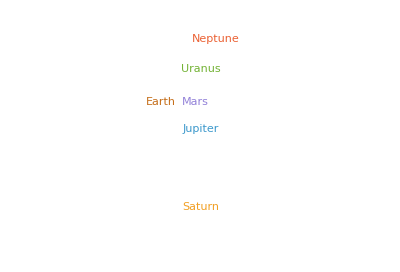

```mathematica
(* 45.1 *) WordCloud[planets[All,"Moons",Length]]
```

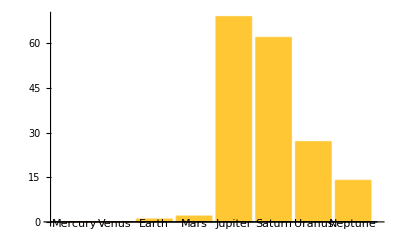

```mathematica
(* 45.2 *)BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

```mathematica
(* 45.3 *)planetsSortedByNumberOfMoonsDescending=Reverse[planets[SortBy[Length[#Moons]&]]];
planetsSortedByNumberOfMoonsDescending[All,"Mass"]
```

```mathematica
(* 45.4 *) planets[All,"Moons",Max,"Mass"]
```

```mathematica
(* 45.5 *) Sort[planets[All,"Moons",Max,"Mass"]]
(* How am I supposed to get the planet masses back into the table? *)
```

```mathematica
(* 45.6 *) planets[All,"Moons",Median,"Mass"]
```

```mathematica
(* 45.7 *) earthMass=Entity["Planet","Earth"][EntityProperty["Planet","Mass"]];
```

```mathematica
planets[All,"Moons",Select[#Mass>0.0001 earthMass&]]
```

```mathematica
Association
```

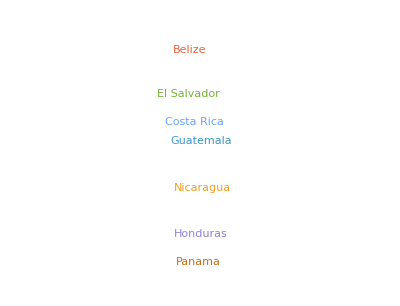

```mathematica
(* 45.8 *) countryNames=EntityClass["Country","CentralAmerica"]["Name"];
WordCloud[Association[#->StringLength[WikipediaData[#]]&/@countryNames]]
```

```mathematica
(* 45.9 *) fireballs=ResourceData["Fireballs and Bolides"]
```

```mathematica
fireballs[Max,"Altitude"]
```

66.6 km

```mathematica
(* 45.10 *) Take[Sort[fireballs[All,"Altitude"]],-5]
```

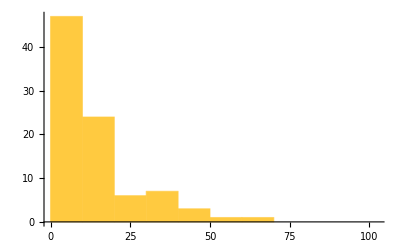

```mathematica
(* 45.11 *) Histogram[Differences[fireballs[All,"PeakBrightness"]]]
```

```mathematica
(* 45.12 *) nearestCities=Interpreter["City"]/@Take[fireballs[All,"NearestCity"],10];
GeoListPlot[Labeled/@nearestCities]
```

-Graphics-

```mathematica
Reverse[fireballs[SortBy[#Altitude &]]]
```

```mathematica
(* 45.13 *)nearestCitiesLargestAltitudes=Interpreter["City"]/@Take[Reverse[fireballs[SortBy[#Altitude &]]],10][All,"NearestCity"];
GeoListPlot[Labeled/@nearestCitiesLargestAltitudes]
```

-Graphics-

## Exercises from EIWL3 Section 46

```mathematica
(* 46.1 *) Spectrogram[SpeechSynthesize[IntegerName[123456]]]
```

-Graphics-

```mathematica
(* 46.2 *) Spectrogram[SpeechSynthesize[SortBy[WordList[],StringLength[#]&][[-1]]]]
```

-Graphics-

```mathematica
(* 46.3 *) spokenAlphabet=SpeechSynthesize[StringRiffle[Alphabet[]," "]]
```

```mathematica
(* 46.4 *) SpeechSynthesize[spokenAlphabet]
```

```mathematica
(* 46.5 *) AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
(* 46.6 *) Table[AudioPitchShift[SpeechSynthesize["computer"],r],{r,1.0,1.5,0.1}]
```

{,,,,,}

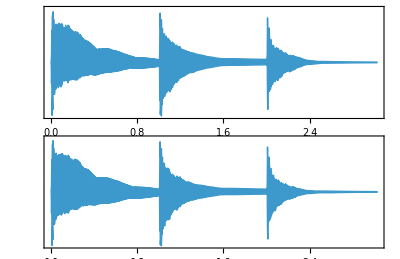

```mathematica
(* 46.7 *) AudioPlot[Sound[Table[SoundNote[note,1,"Guitar"],{note,{0,12,24}}]]]
```

```mathematica
(* 46.8 *) Table[AudioIdentify[AudioPitchShift[SoundNote[0,1,"Trumpet"],r]],{r,0.5,1.0,0.1}]
```

{trombone,trombone,trombone,trumpet,trumpet,trumpet}

```mathematica
(* 46.9 *) foxImage=Entity["TaxonomicSpecies","VulpesVulpes::48y38"][EntityProperty["TaxonomicSpecies","Image"]];
AnimationVideo[Blur[foxImage,20-step],{step,0,20}]
```

```mathematica
(* 46.10 *) AnimationVideo[Graphics[{Circle[],RegularPolygon[vertices]}],{vertices,3,20}]
```

```mathematica
(* 46.11 *) AnimationVideo[Graphics[{Hue[hue],Disk[]},ImageSize->50],{hue,0,1}]
```

```mathematica
(* 46.12 *) AnimationVideo[Graphics[Rasterize[letter,RasterSize->200]],{letter,Capitalize[Alphabet[]]},FrameRate->2]
```